```mathematica
outputdir="/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/one_dimension/solution_ode_solve_nu/";
```

```mathematica
If[DirectoryQ[outputdir],DeleteDirectory[outputdir,DeleteContents->True];Print["Directory deleted"],Print["Directory does not exist"]]
```

Directory deleted

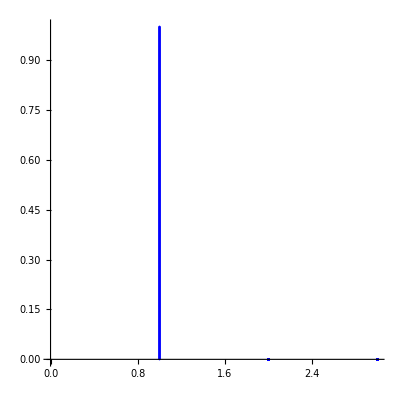

1001

```mathematica
tabve=Import["/Users/michelecastellana/Documents/finite_elements/generate_mesh/1d/line/solution/vertices.csv"]
tabve=Table[tabve[[i]],{i,2,Length[tabve]}]
ListPlot[tabve,PlotStyle->Blue,AspectRatio->1]
Length[tabve]
```

```mathematica
(*write ψ from ODE to csv file*)
```

```mathematica
tabψ=Table[{ψ[x]/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]},{i,1,Length[tabve]}];
PrependTo[tabψ,{"f",":0",":1",":2"}]
```

```mathematica
Export[outputdir<>"psi.csv",tabψ]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/one_dimension/solution_ode_solve_nu/psi.csv

```mathematica
(*write μ from ODE to csv file*)
```

```mathematica
tabμ=Table[{H[x]/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]},{i,1,Length[tabve]}];
PrependTo[tabμ,{"f",":0",":1",":2"}]
```

```mathematica
Export[outputdir<>"mu.csv",tabμ]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/one_dimension/solution_ode_solve_nu/mu.csv

```mathematica
(*write u from ODE to csv file*)
```

```mathematica
tabu=Table[Flatten[{{X1[x]-Xref[x][[1]],X2[x]-Xref[x][[2]],0}/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]}],{i,1,Length[tabve]}];
PrependTo[tabu,{"f:0","f:1","f:2",":0",":1",":2"}]
```

```mathematica
Export[outputdir<>"u.csv",tabu]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/one_dimension/solution_ode_solve_nu/u.csv

```mathematica
(*write ν from ODE to csv file*)
```

```mathematica
tabν=Table[{ν[x]/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]},{i,1,Length[tabve]}];
PrependTo[tabν,{"f",":0",":1",":2"}]
```

```mathematica
Export[outputdir<>"nu.csv",tabν]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/one_dimension/solution_ode/nu.csv